## Aufgabe 96

### Überblick

```mathematica
f[x_,y_]:=x^3+y^3-3x y
```

Funktionsgraph und Höhenschichtlinien

-Graphics3D-

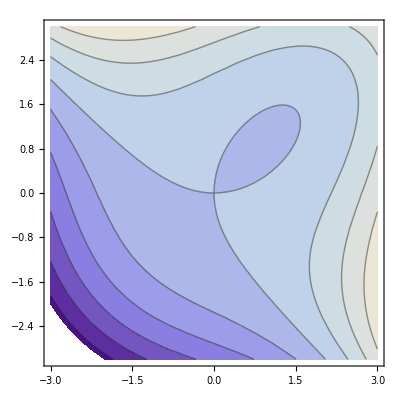

```mathematica
Plot3D[f[x,y],{x,-3,3},{y,-3,3}]
ContourPlot[f[x,y],{x,-3,3},{y,-3,3}]
```

Vermutung : Sattel in (0, 0), lok. Min nahe (1, 1), keine globalen Extrema

### Kritische Punkte

```mathematica
Gradf={D[f[x,y],x],D[f[x,y],y]}
```

{3 x^2-3 y,-3 x+3 y^2}

```mathematica
Solve[Gradf=={0,0},{x,y}]
```

{{x→0,y→0},{x→1,y→1},{x→-(-1)^(1/3),y→(-1)^(2/3)},{x→(-1)^(2/3),y→-(-1)^(1/3)}}

Wir suchen natürlich nur reelle Lösungen, also :
  K1 = (0, 0), K2 = (1, 1)

### Auswertung der Hesse Matrix

```mathematica
Hessf=MatrixForm[{{D[f[x,y],{x,2}],D[D[f[x,y],x],y]},{D[D[f[x,y],x],y],D[f [x,y],{y,2}]}}]
```

(6 x | -3
-3 | 6 y)

```mathematica
Hessf/.{x->0,y->0}
```

(0 | -3
-3 | 0)

```mathematica
Det[%]
```

-9

Indefinit, also :
   K1 = (0, 0) ist ein Sattel

```mathematica
Hessf/.{x->1,y->1}
```

(6 | -3
-3 | 6)

```mathematica
Det[%]
```

27

Determinante positiv und (1, 1 - Eintrag prositiv = > Hesse Matrix pos. definit, also :
    K2 = (1, 1) ist lok. Minimum

## Aufgabe 97

### Überblick

```mathematica
f[x_,y_]:=3x Exp[y]-x^3-Exp[3y]
```

Funktionsgraph und Höhenschichtlinien

-Graphics3D-

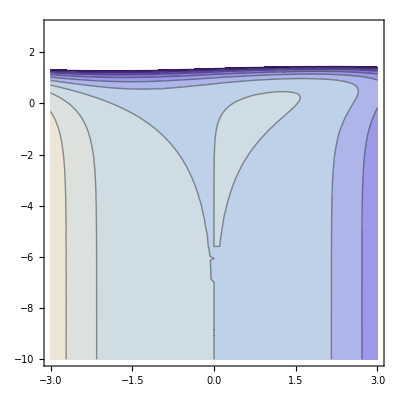

```mathematica
Plot3D[f[x,y],{x,-1.5,1.5},{y,-1.5,1.5}]
ContourPlot[f[x,y],{x,-3,3},{y,-10,3}]
```

Vermutung : Lok. Max nahe (1,0) , keine globalen Extrema

### Kritische Punkte

```mathematica
Gradf={D[f[x,y],x],D[f[x,y],y]}
```

{3 ⅇ^y-3 x^2,-3 ⅇ^(3 y)+3 ⅇ^y x}

```mathematica
Solve[Gradf=={0,0},{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0,y→-∞},{x→1,y→0},{x→-(-1)^(1/3),y→(2 ⅈ π)/3},{x→(-1)^(2/3),y→-(2 ⅈ π)/3}}

Wir suchen natürlich nur reelle Lösungen, also :
  K1 = (1,0)

### Auswertung der Hesse Matrix

```mathematica
Hessf=MatrixForm[{{D[f[x,y],{x,2}],D[D[f[x,y],x],y]},{D[D[f[x,y],x],y],D[f [x,y],{y,2}]}}]
```

(-6 x | 3 ⅇ^y
3 ⅇ^y | -9 ⅇ^(3 y)+3 ⅇ^y x)

```mathematica
Hessf/.{x->1,y->0}
```

(-6 | 3
3 | -6)

```mathematica
Det[%]
```

27

Determinante positiv und (1, 1) - Eintrag negativ = > Hesse Matrix neg. definit, also :
    K1 = (1, 0) ist lok. Max.

## Aufgabe 98

### Überblick

```mathematica
f[x_,y_]:=3x^2+x^3-4y^3-y^4
```

Funktionsgraph und Höhenschichtlinien

-Graphics3D-

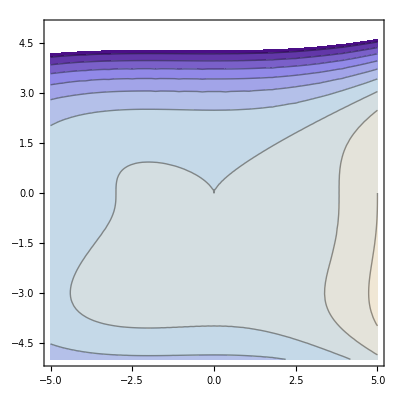

```mathematica
Plot3D[f[x,y],{x,-4,4},{y,-4,4}]
ContourPlot[f[x,y],{x,-5,5},{y,-5,5}]
```

Vermutung : Sattel in (0, 0), links des Ursprungs und auch unterhalb des Ursprungs, lok. Max nahe (-2, -3), keine globalen Extrema

### Kritische Punkte

```mathematica
Gradf={D[f[x,y],x],D[f[x,y],y]}
```

{6 x+3 x^2,-12 y^2-4 y^3}

```mathematica
Solve[Gradf=={0,0},{x,y}]
```

{{x→-2,y→-3},{x→0,y→-3},{x→-2,y→0},{x→0,y→0}}

Vier kritische Punkte:
  K1 = (0, 0), K2 = (-2, 0), K3=(0,-3), K4=(-2,-3)

### Auswertung der Hesse Matrix

```mathematica
Hessf=MatrixForm[{{D[f[x,y],{x,2}],D[D[f[x,y],x],y]},{D[D[f[x,y],x],y],D[f [x,y],{y,2}]}}]
```

(6+6 x | 0
0 | -24 y-12 y^2)

```mathematica
Hessf/.{x->0,y->0}
```

(6 | 0
0 | 0)

```mathematica
Eigenvalues[%]
```

{6,0}

Positiv Semidefinit, also :
   K1 = (0, 0) ist ein Sattel

```mathematica
Hessf/.{x->-2,y->0}
```

(-6 | 0
0 | 0)

```mathematica
Eigenvalues[%]
```

{-6,0}

Negativ Semidefinit, also :
   K2 = (-2, 0) ist ein Sattel

```mathematica
Hessf/.{x->-0,y->-3}
```

(6 | 0
0 | -36)

```mathematica
Eigenvalues[%]
```

{-36,6}

Indefinit, also :
   K3 = (0, -3) ist ein Sattel

```mathematica
Hessf/.{x->-2,y->-3}
```

(-6 | 0
0 | -36)

```mathematica
Eigenvalues[%]
```

{-36,-6}

Negativ definit, also :
   K4 = (-2, -3) ist ein lok. Max.

## Aufgabe 99

### Überblick

```mathematica
f[x_,y_]:=x+y
```

Funktionsgraph und Höhenschichtlinien

-Graphics3D-

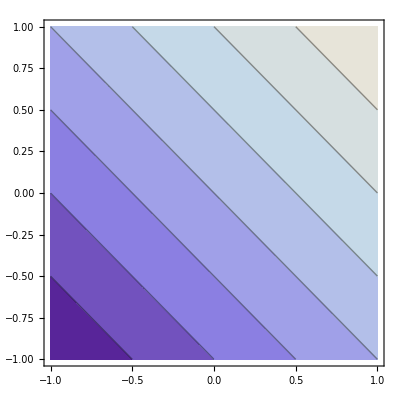

```mathematica
Plot3D[f[x,y],{x,-1,1},{y,-1,1}]
ContourPlot[f[x,y],{x,-1,1},{y,-1,1}]
```

### Methode 1 : Einsetzen (“Wie in der Schule”)

```mathematica
f1[x_]:=x+Sqrt[1-x^2]
f2[x_]:=x-Sqrt[1-x^2]
```

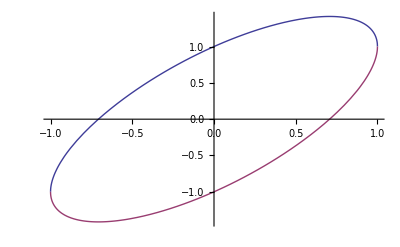

```mathematica
Plot[{f1[x],f2[x]},{x,-1,1}]
```

```mathematica
Solve[f1'[x]==0,x]
f1''[x]
```

{{x→1/(√2)}}

-x^2/((1-x^2)^(3/2))-1/(√(1-x^2))

f1'' < 0 also lok. Max. in x = 1/Sqrt[2]
Dh insgesamt lok. Max. in (x, y) = (1/Sqrt[2], 1/Sqrt[2])

```mathematica
Solve[f2'[x]==0,x]
f2''[x]
```

{{x→-1/(√2)}}

x^2/((1-x^2)^(3/2))+1/(√(1-x^2))

```mathematica
f2'' > 0 also lok. Min. in x = -1/Sqrt[2]
Dh insgesamt lok. Min. in (x, y) = (-1/Sqrt[2],-1/Sqrt[2])
```

### Methode 2 : Lagrange Multiplikatoren

```mathematica
g[x_,y_]:=x^2+y^2-1
h[x_,y_,λ_]:=f[x,y]-λ*g[x,y]
h[x,y,λ]
{D[h[x,y,λ],x],D[h[x,y,λ],y],D[h[x,y,λ],λ]}
```

x+y-(-1+x^2+y^2) λ

{1-2 x λ,1-2 y λ,1-x^2-y^2}

```mathematica
Solve[%==0,{x,y,λ}]
```

{{x→-1/(√2),y→-1/(√2),λ→-1/(√2)},{x→1/(√2),y→1/(√2),λ→1/(√2)}}

Also Kandidaten für lok. Extr.  K1, 2 = (x, y) = +/-(1/Sqrt[2], 1/Sqrt[2])
Da S^1 kompakt muss es ein lok = glob Max und Min geben. Also reicht ein Vergleich der Funktionswerte an den Kanidadatenstellen.

```mathematica
f[1/Sqrt[2],1/Sqrt[2]]
f[-1/Sqrt[2],-1/Sqrt[2]]
```

√2

-√2

Also lok. = glob. Max in K1, Min in K2

## Aufgabe 100

### Überblick

```mathematica
f[x_,y_]:=x^2 y
```

Funktionsgraph und Höhenschichtlinien

-Graphics3D-

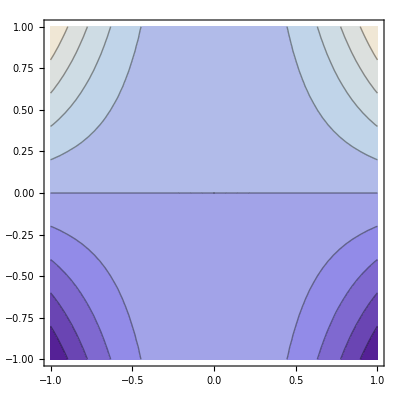

```mathematica
Plot3D[f[x,y],{x,-1,1},{y,-1,1}]
ContourPlot[f[x,y],{x,-1,1},{y,-1,1}]
```

Vermute nicht strikte lok. Max./Min. auf der neg./pos. y - Achse und kein lok. Extr. in (0, 0)

### (a) Max/Min auf offener Einheitskreisscheibe

#### Kritische Punkte

```mathematica
Gradf={D[f[x,y],x],D[f[x,y],y]}
```

{2 x y,x^2}

```mathematica
Solve[Gradf=={0,0},{x,y}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{x→0}}

Die ganze y-Achse besteht aus krit. Punkten

#### Auswertung der Hesse Matrix

```mathematica
Hessf=MatrixForm[{{D[f[x,y],{x,2}],D[D[f[x,y],x],y]},{D[D[f[x,y],x],y],D[f [x,y],{y,2}]}}]
```

(2 y | 2 x
2 x | 0)

```mathematica
Hessf/.{x->0}
```

(2 y | 0
0 | 0)

Nie definit und Det = 0 also auch nicht indefinit = > KEINE AUSSAGE MÖGLICH
Ausweg:

#### Diskutiere Vorzeichen

f = 0 auf der y - Achse
f >= 0 in oberer Halbebene
f <= 0 in unterer Halbebene

Daher nichtstrikte lok Min/Max auf pos/neg y - Achse.
   Kein lok. Extremum in (0, 0)

### (b) Auf Einheitskreis

```mathematica
Methode 1: Einsetzen
```

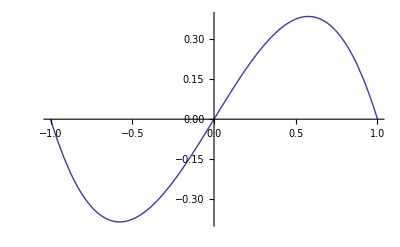

```mathematica
f1[y_]:=y (1-y^2)
Plot[f1[y],{y,-1,1}]
```

Weil auf [-1, 1] zu diskutieren (!! !)
lok. Max./Min in - /+1

```mathematica
Solve[f1'[y ]==0,y]
```

{{y→-1/(√3)},{y→1/(√3)}}

```mathematica
f1''[1/Sqrt[3]]
f1''[-1/Sqrt[3]]
```

-2 √3

2 √3

Daher lok. Max./Min. in + /-1/Sqrt[3]

Daher insgesamt lok. Max./Min.(auch global) in
(+/-Sqrt[2/3], 1/Sqrt[3]) / (+/-Sqrt[2/3], -1/Sqrt[3])
und lok. Max./Min. in (0,-/+1)

## Aufgabe 101

Zwei Skizzen zur Illustration :

```mathematica
Plot3D[{Sqrt[(1-y^2-x^2)/2],-Sqrt[(1-y^2-x^2)/2],x+y},{x,-1,1},{y,-1,1}]
```

-Graphics3D-

```mathematica
Plot3D[{Sqrt[(1-y^2-x^2)/2],-Sqrt[(1-y^2-x^2)/2],x+y},{x,-1,1},{y,-1,1}]
```

-Graphics3D-